```mathematica
SetDirectory@NotebookDirectory[]
```

/home/matt/datadrop/Dropbox/Berman-Research/cluster/phos

```mathematica
Import["neatphos.m"]
mx=mus[[1,1]];
my=mus[[1,2]];
```

#### Modified ndespolar to avoid the ArcTan[Tan[θ]] thing

```mathematica
ndespolar[3, mx, my, VKeld, 4.89, chiphos, 0, 4*10^-4,10^12,None]
```

{{-0.0069293-2.00731×10^-13 ⅈ,-0.00299941+1.60316×10^-10 ⅈ,-0.00198144-2.59257×10^-8 ⅈ},{InterpolatingFunction[{{0., 1.5708}, {-1.5708, 1.5708}}, <>],InterpolatingFunction[{{0., 1.5708}, {-1.5708, 1.5708}}, <>],InterpolatingFunction[{{0., 1.5708}, {-1.5708, 1.5708}}, <>]}}

```mathematica
ndes[3, mx, my, VKeld, 4.89, chiphos, 0, 4*10^-4,10^12,None]
```

{{-0.00689082,-0.00293256,-0.00195747},{InterpolatingFunction[{{-1.5708, 1.5708}, {-1.5708, 1.5708}}, <>],InterpolatingFunction[{{-1.5708, 1.5708}, {-1.5708, 1.5708}}, <>],InterpolatingFunction[{{-1.5708, 1.5708}, {-1.5708, 1.5708}}, <>]}}

```mathematica
Table[
cartev=ndes[3, mx, my, VKeld, 4.89, chiphos, 0, eps,10^12,None][[1]];
polaev=ndespolar[3, mx, my, VKeld, 4.89, chiphos, 0, eps,10^12,None][[1]];
{
UnitConvert[Quantity[cartev,"Hartrees"],"Millielectronvolts"],
UnitConvert[Quantity[polaev,"Hartrees"],"Millielectronvolts"],
UnitConvert[Quantity[Abs[polaev],"Hartrees"],"Millielectronvolts"]
}
,
{eps,{4*10^-4,8*10^-5,6*10^-5,2*10^-5}}
]
%//TableForm
```

NDEigensystem::femdpop: The NDSolve`FEM`FEMStiffnessElements operator failed.

{{{-187.509 meV,-79.799 meV,-53.2656 meV},{(-188.556-5.46216×10^-9 ⅈ) meV,(-81.6182+4.36243×10^-6 ⅈ) meV,(-53.9177-0.000705475 ⅈ) meV},{188.556 meV,81.6182 meV,53.9177 meV}},{{-187.989 meV,-78.5483 meV,-53.6914 meV},{(-188.059-3.04737×10^-9 ⅈ) meV,(-78.7816+0.0000679917 ⅈ) meV,(-54.0501-0.0101406 ⅈ) meV},{188.059 meV,78.7816 meV,54.0501 meV}},{{-187.968 meV,-78.6224 meV,-53.6781 meV},{(-188.006-2.42163×10^-10 ⅈ) meV,(-78.7752-0.0000190303 ⅈ) meV,(-53.995+0.0150837 ⅈ) meV},{188.006 meV,78.7752 meV,53.995 meV}},{{-272114. meV,-272114. meV,-272114. meV},{(-187.949-7.07159×10^-10 ⅈ) meV,(-78.6518-5.6661×10^-6 ⅈ) meV,(-53.9003+0.022399 ⅈ) meV},{187.949 meV,78.6518 meV,53.9003 meV}}}

-187.509 meV
-79.799 meV
-53.2656 meV | (-188.556-5.46216×10^-9 ⅈ) meV
(-81.6182+4.36243×10^-6 ⅈ) meV
(-53.9177-0.000705475 ⅈ) meV | 188.556 meV
81.6182 meV
53.9177 meV
-187.989 meV
-78.5483 meV
-53.6914 meV | (-188.059-3.04737×10^-9 ⅈ) meV
(-78.7816+0.0000679917 ⅈ) meV
(-54.0501-0.0101406 ⅈ) meV | 188.059 meV
78.7816 meV
54.0501 meV
-187.968 meV
-78.6224 meV
-53.6781 meV | (-188.006-2.42163×10^-10 ⅈ) meV
(-78.7752-0.0000190303 ⅈ) meV
(-53.995+0.0150837 ⅈ) meV | 188.006 meV
78.7752 meV
53.995 meV
-272114. meV
-272114. meV
-272114. meV | (-187.949-7.07159×10^-10 ⅈ) meV
(-78.6518-5.6661×10^-6 ⅈ) meV
(-53.9003+0.022399 ⅈ) meV | 187.949 meV
78.6518 meV
53.9003 meV

```mathematica
Table[
ndespolar[6, mx, my, VKeld, 4.89, chiphos, 0, 10^-4,10^mix,None][[1]],
{mix,{3,6,9,12}}
]//TableForm
```

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

$Aborted

```mathematica
minute
```

23

#### Old attempts

```mathematica
tds=(-(1/2)*((1/mx)*D[f[x,y],{x,2},{y,0}]+(1/my)*D[f[x,y],{x,0},{y,2}])+pot[kappa][d,chi][x,y]*f[x,y]+shift*f[x,y])
tdsp=FullSimplify[tds /. {f -> (g[Sqrt[#1^2 + #2^2], ArcTan[#2/#1]] &)} /. {x -> r*Cos[θ], y->r*Sin[θ]}, {0 ≤  θ < 2*Pi, 0 ≤ r < Infinity}]
tdspt=FullSimplify[tdsp /. {g -> (u[ArcTan[#1], #2] &)} /. {r->Tan[ψ]}, {(-Pi/2) < ψ < (Pi/2)}]
SetPrecision[tdspt,50]
```

shift f[x,y]+1/2 (-1.03333 f^(0,2)[x,y]-15.8824 f^(2,0)[x,y])+f[x,y] pot[kappa][d,chi][x,y]

1/r^2(-14.849 Cos[θ] Sin[θ] g^(0,1)[r,ArcTan[Tan[θ]]]+(-4.22892+3.71225 Cos[2 θ]) g^(0,2)[r,ArcTan[Tan[θ]]]+r ((-4.22892+3.71225 Cos[2 θ]) g^(1,0)[r,ArcTan[Tan[θ]]]+(14.849 Cos[θ] Sin[θ]+4.44089×10^-16 Sin[4 θ]) g^(1,1)[r,ArcTan[Tan[θ]]]+r (-4.22892-3.71225 Cos[2 θ]) g^(2,0)[r,ArcTan[Tan[θ]]]+r g[r,ArcTan[Tan[θ]]] (1. shift+1. pot[kappa][d,chi][r Cos[θ],r Sin[θ]])))

Cot[ψ]^2 (-14.849 Cos[θ] Sin[θ] u^(0,1)[ψ,ArcTan[Tan[θ]]]+(-4.22892+3.71225 Cos[2 θ]) u^(0,2)[ψ,ArcTan[Tan[θ]]]+Cos[ψ] Sin[ψ] ((1.64857×10^-15+Cos[2 θ] (7.42451-3.71225 Cos[2 ψ])-4.22892 Cos[2 ψ]) u^(1,0)[ψ,ArcTan[Tan[θ]]]+14.849 Cos[θ] Sin[θ] u^(1,1)[ψ,ArcTan[Tan[θ]]]+(-2.11446-1.85613 Cos[2 θ]) Sin[2 ψ] u^(2,0)[ψ,ArcTan[Tan[θ]]])+Tan[ψ]^2 u[ψ,ArcTan[Tan[θ]]] (1. shift+1. pot[kappa][d,chi][Cos[θ] Tan[ψ],Sin[θ] Tan[ψ]]))

Cot[ψ]^2 (-14.84901960784313956764890463091433048248291015625 Cos[θ] Sin[θ] u^(0,1)[ψ,ArcTan[Tan[θ]]]+(-4.228921568627452387545417877845466136932373046875+3.7122549019607848919122261577285826206207275390625 Cos[2. θ]) u^(0,2)[ψ,ArcTan[Tan[θ]]]+Cos[ψ] Sin[ψ] ((1.648572346173786625517110841045368472555278111652×10^-15+Cos[2. θ] (7.4245098039215715601812917157076299190521240234375-3.7122549019607848919122261577285826206207275390625 Cos[2. ψ])-4.228921568627452387545417877845466136932373046875 Cos[2. ψ]) u^(1,0)[ψ,ArcTan[Tan[θ]]]+14.84901960784313956764890463091433048248291015625 Cos[θ] Sin[θ] u^(1,1)[ψ,ArcTan[Tan[θ]]]+(-2.1144607843137261937727089389227330684661865234375-1.8561274509803924459561130788642913103103637695313 Cos[2. θ]) Sin[2. ψ] u^(2,0)[ψ,ArcTan[Tan[θ]]])+Tan[ψ]^2 u[ψ,ArcTan[Tan[θ]]] (1. shift+1. pot[kappa][d,chi][Cos[θ] Tan[ψ],Sin[θ] Tan[ψ]]))

Better to make domain of θ [-Pi/2 , Pi/2]?

```mathematica
tds=(-(1/2)*((1/mx)*D[f[x,y],{x,2},{y,0}]+(1/my)*D[f[x,y],{x,0},{y,2}])+pot[kappa][d,chi][x,y]*f[x,y]+shift*f[x,y])
tdsp=FullSimplify[tds /. {f -> (g[Sqrt[#1^2 + #2^2], ArcTan[#2/#1]] &)} /. {x -> r*Cos[θ], y->r*Sin[θ]}, {-Pi/2 ≤  θ < Pi/2, 0 ≤ r < Infinity}]
tdspt=FullSimplify[tdsp /. {g -> (u[ArcTan[#1], #2] &)} /. {r->Tan[ψ]}, {(-Pi/2) < ψ < (Pi/2)}]
```

shift f[x,y]+1/2 (-1.03333 f^(0,2)[x,y]-15.8824 f^(2,0)[x,y])+f[x,y] pot[kappa][d,chi][x,y]

1/r^2(-14.849 Cos[θ] Sin[θ] g^(0,1)[r,ArcTan[Tan[θ]]]+(-4.22892+3.71225 Cos[2 θ]) g^(0,2)[r,ArcTan[Tan[θ]]]+r ((-4.22892+3.71225 Cos[2 θ]) g^(1,0)[r,ArcTan[Tan[θ]]]+(14.849 Cos[θ] Sin[θ]+4.44089×10^-16 Sin[4 θ]) g^(1,1)[r,ArcTan[Tan[θ]]]+r (-4.22892-3.71225 Cos[2 θ]) g^(2,0)[r,ArcTan[Tan[θ]]]+r g[r,ArcTan[Tan[θ]]] (1. shift+1. pot[kappa][d,chi][r Cos[θ],r Sin[θ]])))

Cot[ψ]^2 (-14.849 Cos[θ] Sin[θ] u^(0,1)[ψ,ArcTan[Tan[θ]]]+(-4.22892+3.71225 Cos[2 θ]) u^(0,2)[ψ,ArcTan[Tan[θ]]]+Cos[ψ] Sin[ψ] ((1.64857×10^-15+Cos[2 θ] (7.42451-3.71225 Cos[2 ψ])-4.22892 Cos[2 ψ]) u^(1,0)[ψ,ArcTan[Tan[θ]]]+14.849 Cos[θ] Sin[θ] u^(1,1)[ψ,ArcTan[Tan[θ]]]+(-2.11446-1.85613 Cos[2 θ]) Sin[2 ψ] u^(2,0)[ψ,ArcTan[Tan[θ]]])+Tan[ψ]^2 u[ψ,ArcTan[Tan[θ]]] (1. shift+1. pot[kappa][d,chi][Cos[θ] Tan[ψ],Sin[θ] Tan[ψ]]))

```mathematica
tdspt//Head
```

Times

## Testing ndespolar

#### Setup

```mathematica
mx=mus[[1,1]]
my=mus[[1,2]]
```

0.062963

0.967742

#### OG xy

```mathematica
ndes[3, mx, my, VKeld, 4.89, chiphos, 0, 10^-3,10^12,None]
```

{{-0.00703532,-0.00295092,-0.00156342},{InterpolatingFunction[{{-1.5708, 1.5708}, {-1.5708, 1.5708}}, <>],InterpolatingFunction[{{-1.5708, 1.5708}, {-1.5708, 1.5708}}, <>],InterpolatingFunction[{{-1.5708, 1.5708}, {-1.5708, 1.5708}}, <>]}}

```mathematica
Table[
{
ndes[3, mx, my, VKeld, 4.89, chiphos, 0, eps,10^12,None][[1]],
ndespolar[3, mx, my, VKeld, 4.89, chiphos, 0, eps,10^12,None][[1]]
}, 
{eps,{10^-3,4*10^-4,8*10^-5}}
]
```

NDEigensystem::femdpop: The NDSolve`FEM`FEMStiffnessElements operator failed.

NDEigensystem::maxeigen: A maximum number of 0 eigenvalues and functions can be computed for this discretized system.

Set::shape: Lists {evs$501473,efs$501473} and NDEigensystem[{(10+0.0322669 BesselY[0,Times[«2»]]-0.0322669 StruveH[0,Times[«2»]]) u[ξ,ψ]+(1.03333 Tan[ψ] u^(0,1)[ξ,ψ])/((1.+Tan[«1»]^2)^2)-(0.516667 u^(0,2)[ξ,ψ])/((1.+Tan[«1»]^2)^2)+(15.8824 Tan[ξ] u^(1,0)[ξ,ψ])/((1.+Tan[«1»]^2)^2)-(7.94118 u^(2,0)[ξ,ψ])/((1.+Tan[«1»]^2)^2),DirichletCondition[u[ξ,ψ]==0,Abs[ξ]==1.5708||Abs[ψ]==1.5708]},«3»,Method→{SpatialDiscretization→{FiniteElement,{MeshOptions→{«1»}}},«1»,Vect…tion→«4»}] are not the same shape.

NDEigensystem::femdpop: The NDSolve`FEM`FEMStiffnessElements operator failed.

General::stop: Further output of NDEigensystem::femdpop will be suppressed during this calculation.

NDEigensystem::maxeigen: A maximum number of 0 eigenvalues and functions can be computed for this discretized system.

NDEigensystem::dvlen: The function u[ψ,ArcTan[Tan[θ]]] does not have the same number of arguments as independent variables (3).

Set::shape: Lists {evs$502812,efs$502812} and NDEigensystem[{Cot[ψ]^2 ((10.+0.0322669 BesselY[«2»]-2.22045×10^-16 Cos[«1»]-0.0322669 StruveH[«2»]) Tan[ψ]^2 u[ψ,ArcTan[Tan[«1»]]]+(-4.22892+3.71225 Cos[«1»]) u^(0,2)[ψ,ArcTan[Tan[«1»]]]+(«1»+«1») «1»+Cos[θ] Sin[θ] (-14.849 («1»)^(«2»)[«2»]+14.849 Cos[«1»] Sin[«1»] («1»)^(«2»)[«2»])+(-2.11446-1.85613 Cos[«1»]+4.16334×10^-17 Cos[«1»]) Cos[ψ] Sin[ψ] Sin[2 ψ] u^(2,0)[ψ,ArcTan[Tan[«1»]]]),«1»},«4»] are not the same shape.

$Aborted

```mathematica
ndespolar[3, mx, my, VKeld, 4.89, chiphos, 0, 4*10^-4,10^12,None]
```

NDEigensystem::femcnsd: The PDE coefficient 1. Cot[ψ]^2 («1») does not evaluate to a numeric scalar at the coordinate {π/4,-π/2}; it evaluated to 1. (0.+9.94853 y[0.785398,-1.5708]-7.94118 y^(0,2)[0.785398,-1.5708]+0.5 (-7.42451 y^(1,0)[0.785398,-1.5708]+(0.+4.5854×10^-16 ⅈ) y^(1,1)[0.785398,-1.5708]-0.258333 y^(2,0)[0.785398,-1.5708])) instead.

General::stop: Further output of NDEigensystem::femcnsd will be suppressed during this calculation.

Set::shape: Lists {evs$179644,efs$179644} and NDEigensystem[{Cot[ψ]^2 ((10.+0.0322669 BesselY[«2»]-2.22045×10^-16 Cos[«1»]-0.0322669 StruveH[«2»]) Tan[ψ]^2 y[ψ,θ]-14.849 Cos[θ] Sin[θ] y^(0,1)[ψ,θ]+(-4.22892+3.71225 Cos[«1»]) y^(0,2)[ψ,θ]+Cos[ψ] Sin[ψ] (Plus[«3»] («1»)^(«2»)[«2»]+Plus[«2»] («1»)^(«2»)[«2»]+Plus[«3»] Sin[«1»] («1»)^(«2»)[«2»])),DirichletCondition[u[ψ,θ]==0,ψ==π/2]},«3»,Method→{SpatialDiscretization→{FiniteElement,{MeshOptions→{«1»}}},Eig…tem→«1»,VectorNormalization→None}] are not the same shape.

{-10+evs$179644,efs$179644}

```mathematica
tdsptr=tdspt/.{shift->10,pot->VKeld,chi->chiphos,kappa->4.89,d->0}
```

-4.10294 Cot[ψ]^2 (-0.243728 (10-0.0322669 (-BesselY[0,0.100449 √(Cos[θ]^2 Tan[ψ]^2+Sin[θ]^2 Tan[ψ]^2)]+StruveH[0,0.100449 √(Cos[θ]^2 Tan[ψ]^2+Sin[θ]^2 Tan[ψ]^2)])) Tan[ψ]^2 u[ψ,ArcTan[Tan[θ]]]-0.904779 Sin[2 θ] (-2 u^(0,1)[ψ,ArcTan[Tan[θ]]]+Sin[2 ψ] u^(1,1)[ψ,ArcTan[Tan[θ]]])-0.113097 Cos[2 θ] (8 u^(0,2)[ψ,ArcTan[Tan[θ]]]-4 (-2+Cos[2 ψ]) Sin[2 ψ] u^(1,0)[ψ,ArcTan[Tan[θ]]]+(-1+Cos[4 ψ]) u^(2,0)[ψ,ArcTan[Tan[θ]]])+0.257676 (4 u^(0,2)[ψ,ArcTan[Tan[θ]]]+Sin[4 ψ] u^(1,0)[ψ,ArcTan[Tan[θ]]]+Sin[2 ψ]^2 u^(2,0)[ψ,ArcTan[Tan[θ]]]))

```mathematica
NDEigensystem[
{
Function[{ψ,θ},Evaluate[tdspt/.{shift->10,pot->VKeld,chi->chiphos,kappa->4.89,d->0}]],
DirichletCondition[u[ψ,θ]==0,ψ==(pio2)]
},
u[ψ,θ],
{ψ,θ}∈Rectangle[{0,-Pi/2},{Pi/2,Pi/2}],
4,
Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->10^-4}}},"Eigensystem"->{"Arnoldi","MaxIterations"->10^12},"VectorNormalization"->None}
]
```

NDEigensystem::dvlen: The function u[ψ,ArcTan[Tan[θ]]] does not have the same number of arguments as independent variables (3).

NDEigensystem[{Function[{ψ,θ},-4.10294 Cot[ψ]^2 (-0.243728 (10-0.0322669 (-BesselY[0,0.100449 √(Cos[θ]^2 Tan[ψ]^2+Sin[θ]^2 Tan[ψ]^2)]+StruveH[0,0.100449 √(Cos[θ]^2 Tan[ψ]^2+Sin[θ]^2 Tan[ψ]^2)])) Tan[ψ]^2 u[ψ,ArcTan[Tan[θ]]]-0.904779 Sin[2 θ] (-2 u^(0,1)[ψ,ArcTan[Tan[θ]]]+Sin[2 ψ] u^(1,1)[ψ,ArcTan[Tan[θ]]])-0.113097 Cos[2 θ] (8 u^(0,2)[ψ,ArcTan[Tan[θ]]]-4 (-2+Cos[2 ψ]) Sin[2 ψ] u^(1,0)[ψ,ArcTan[Tan[θ]]]+(-1+Cos[4 ψ]) u^(2,0)[ψ,ArcTan[Tan[θ]]])+0.257676 (4 u^(0,2)[ψ,ArcTan[Tan[θ]]]+Sin[4 ψ] u^(1,0)[ψ,ArcTan[Tan[θ]]]+Sin[2 ψ]^2 u^(2,0)[ψ,ArcTan[Tan[θ]]]))],DirichletCondition[u[ψ,θ]==0,ψ==pio2]},u[ψ,θ],{ψ,θ}∈Rectangle[{0,-π/2},{π/2,π/2}],4,Method→{SpatialDiscretization→{FiniteElement,{MeshOptions→{MaxCellMeasure→1/10000}}},Eigensystem→{Arnoldi,MaxIterations→1000000000000},VectorNormalization→None}]

```mathematica
Function[{ψ,θ},Evaluate[tdspt/.{shift->10,pot->VKeld,chi->chiphos,kappa->4.89,d->0}]]
```

Function[{ψ,θ},-4.10294 Cot[ψ]^2 (-0.243728 (10-0.0322669 (-BesselY[0,0.100449 √(Cos[θ]^2 Tan[ψ]^2+Sin[θ]^2 Tan[ψ]^2)]+StruveH[0,0.100449 √(Cos[θ]^2 Tan[ψ]^2+Sin[θ]^2 Tan[ψ]^2)])) Tan[ψ]^2 u[ψ,ArcTan[Tan[θ]]]-0.904779 Sin[2 θ] (-2 u^(0,1)[ψ,ArcTan[Tan[θ]]]+Sin[2 ψ] u^(1,1)[ψ,ArcTan[Tan[θ]]])-0.113097 Cos[2 θ] (8 u^(0,2)[ψ,ArcTan[Tan[θ]]]-4 (-2+Cos[2 ψ]) Sin[2 ψ] u^(1,0)[ψ,ArcTan[Tan[θ]]]+(-1+Cos[4 ψ]) u^(2,0)[ψ,ArcTan[Tan[θ]]])+0.257676 (4 u^(0,2)[ψ,ArcTan[Tan[θ]]]+Sin[4 ψ] u^(1,0)[ψ,ArcTan[Tan[θ]]]+Sin[2 ψ]^2 u^(2,0)[ψ,ArcTan[Tan[θ]]]))]

```mathematica
Laplacian[f[r,θ],{r,θ},"Polar"]
```

(f^(0,2)[r,θ])/r^2+(f^(1,0)[r,θ])/r+f^(2,0)[r,θ]

```mathematica
Simplify[-(1/2)*((1/mx)*D[f[x,y],{x,2},{y,0}]+(1/my)*D[f[x,y],{x,0},{y,2}])/.{f->(u[Sqrt[#1^2+#2^2],ArcTan[#2/#1]]&)}/.{x->r*Cos[θ],y->r*Sin[θ]},{-Pi/2 ≤ θ <Pi/2&&0 ≤ r < Infinity}]
```

1/r^2(-14.849 Cos[θ] Sin[θ] u^(0,1)[r,ArcTan[Tan[θ]]]+(-4.22892+3.71225 Cos[2 θ]-1.10206×10^-16 Cos[4 θ]) u^(0,2)[r,ArcTan[Tan[θ]]]+r ((-4.22892+3.71225 Cos[2 θ]-2.20412×10^-16 Cos[4 θ]+1.65309×10^-16 Cos[6 θ]) u^(1,0)[r,ArcTan[Tan[θ]]]+14.849 Cos[θ] Sin[θ] u^(1,1)[r,ArcTan[Tan[θ]]]+r (-4.22892-3.71225 Cos[2 θ]+5.5103×10^-17 Cos[4 θ]-3.78833×10^-17 Cos[6 θ]) u^(2,0)[r,ArcTan[Tan[θ]]]))

Just x - somehow here we’ve removed the ArcTan[Tan[θ]] stuff

```mathematica
Simplify[Simplify[-(1/(2*Subscript[μ, x]))*D[f[x,y],{x,2},{y,0}]]/.{f->(u[Sqrt[#1^2+#2^2],ArcTan[#2/#1]]&)}/.{x->r*Cos[θ],y->r*Sin[θ]},{-Pi/2<θ<Pi/2,0≤r<Infinity}]
```

-1/(2 r^2 μ_(r Cos[θ]))Cos[θ]^2 (2 Tan[θ] u^(0,1)[r,θ]+Tan[θ]^2 u^(0,2)[r,θ]+r (Tan[θ]^2 u^(1,0)[r,θ]-2 Tan[θ] u^(1,1)[r,θ]+r u^(2,0)[r,θ]))

```mathematica
FullSimplify[
Simplify[
(-1/(2*μx))*D[f[x,y],{x,2},{y,0}]+(-1/(2*μy))*D[f[x,y],{x,0},{y,2}]+V[x,y]*f[x,y]+10*f[x,y]
]/.{
f->(u[Sqrt[#1^2+#2^2],ArcTan[#2/#1]]&)}/.{
x->r*Cos[θ],y->r*Sin[θ]
},
{-Pi/2<θ<Pi/2,0≤r<Infinity}
]
```

-1/(4 r^2 μx μy)(-4 r^2 μx μy u[r,θ] (10+V[r Cos[θ],r Sin[θ]])-2 (μx-μy) Sin[2 θ] (u^(0,1)[r,θ]-r u^(1,1)[r,θ])+(μx-μy) Cos[2 θ] (u^(0,2)[r,θ]+r (u^(1,0)[r,θ]-r u^(2,0)[r,θ]))+(μx+μy) (u^(0,2)[r,θ]+r (u^(1,0)[r,θ]+r u^(2,0)[r,θ])))

This looks promising

```mathematica
FullSimplify[
Simplify[
((-1/(2*μx))*D[f[x,y],{x,2},{y,0}])+((-1/(2*μy))*D[f[x,y],{x,0},{y,2}])+VKeld[kappa][d,chi][x,y]*f[x,y]+10*f[x,y]
]/.{
f->(u[Sqrt[#1^2+#2^2],ArcTan[#2/#1]]&)}/.{
x->r*Cos[θ],y->r*Sin[θ]
},
{-Pi/2<θ<Pi/2,0≤r<Infinity}
]
```

1/4 (((40 chi+BesselY[0,(kappa √(d^2+r^2))/(2 chi π)]-StruveH[0,(kappa √(d^2+r^2))/(2 chi π)]) u[r,θ])/chi-1/(r^2 μx μy)(-2 (μx-μy) Sin[2 θ] (u^(0,1)[r,θ]-r u^(1,1)[r,θ])+(μx-μy) Cos[2 θ] (u^(0,2)[r,θ]+r (u^(1,0)[r,θ]-r u^(2,0)[r,θ]))+(μx+μy) (u^(0,2)[r,θ]+r (u^(1,0)[r,θ]+r u^(2,0)[r,θ]))))

Now do Tan transformation

```mathematica
FullSimplify[
FullSimplify[
Simplify[
((-1/(2*mx))*D[f[x,y],{x,2},{y,0}])+((-1/(2*my))*D[f[x,y],{x,0},{y,2}])+VKeld[kappa][d,chi][x,y]*f[x,y]+10*f[x,y]
]/.{
f->(u[Sqrt[#1^2+#2^2],ArcTan[#2/#1]]&)}/.{
x->r*Cos[θ],y->r*Sin[θ]
},
{-Pi/2<θ<Pi/2,0≤r<Infinity}
]/.{u->(y[ArcTan[#1],#2]&)}/.{r->Tan[ψ]},
{0≤ψ<Pi/2}
]
```

1/chi(10. chi+BesselY[0,(kappa √(d^2+Tan[ψ]^2))/(2 chi π)] (0.25-6.93889×10^-18 Cos[4 θ])+(-0.25+6.93889×10^-18 Cos[4 θ]) StruveH[0,(kappa √(d^2+Tan[ψ]^2))/(2 chi π)]) y[ψ,θ]+Cot[ψ]^2 (-14.849 Cos[θ] Sin[θ] y^(0,1)[ψ,θ]+(-4.22892+3.71225 Cos[2 θ]) y^(0,2)[ψ,θ]+Cos[ψ] Sin[ψ] ((4.22892+(-8.45784+3.71225 Cos[2 θ]) Cos[ψ]^2+(11.1368 Cos[2 θ]-2.77556×10^-16 Cos[6 θ]) Sin[ψ]^2) y^(1,0)[ψ,θ]+(14.849 Cos[θ] Sin[θ]-4.44089×10^-16 Sin[4 θ]) y^(1,1)[ψ,θ]+(-4.22892-3.71225 Cos[2 θ]+2.22045×10^-16 Cos[4 θ]+8.32667×10^-17 Cos[6 θ]) Cos[ψ] Sin[ψ] y^(2,0)[ψ,θ]))

### Looks like the problem might be the ArcTan[Tan[θ]] in the function argument?

```mathematica
tds=(((-1/(2*mx))*D[f[x,y],{x,2},{y,0}]+(-1/(2*my))*D[f[x,y],{x,0},{y,2}])+pot[kappa][d,chi][x,y]*f[x,y]+shift*f[x,y])
tdsp=FullSimplify[Simplify[tds] /. {f -> (g[Sqrt[#1^2 + #2^2], ArcTan[#2/#1]] &)} /. {x -> r*Cos[θ], y->r*Sin[θ]}, {0 ≤  θ < 2*Pi, 0 ≤ r < Infinity}]
tdspt=FullSimplify[tdsp /. {g -> (u[ArcTan[#1], #2] &)} /. {r->Tan[ψ]}, {(-Pi/2) < ψ < (Pi/2)}]
```

shift f[x,y]-0.516667 f^(0,2)[x,y]-7.94118 f^(2,0)[x,y]+f[x,y] pot[kappa][d,chi][x,y]

1/r^2(-14.849 Cos[θ] Sin[θ] g^(0,1)[r,ArcTan[Tan[θ]]]+(-4.22892+3.71225 Cos[2 θ]) g^(0,2)[r,ArcTan[Tan[θ]]]+r ((-4.22892+3.71225 Cos[2 θ]+5.55112×10^-17 Cos[6 θ]) g^(1,0)[r,ArcTan[Tan[θ]]]+14.849 Cos[θ] Sin[θ] g^(1,1)[r,ArcTan[Tan[θ]]]+r (-4.22892-3.71225 Cos[2 θ]+1.66533×10^-16 Cos[4 θ]+2.77556×10^-17 Cos[6 θ]) g^(2,0)[r,ArcTan[Tan[θ]]]+r g[r,ArcTan[Tan[θ]]] (1. shift+1. pot[kappa][d,chi][r Cos[θ],r Sin[θ]])))

Cot[ψ]^2 (-14.849 Cos[θ] Sin[θ] u^(0,1)[ψ,ArcTan[Tan[θ]]]+(-4.22892+3.71225 Cos[2 θ]) u^(0,2)[ψ,ArcTan[Tan[θ]]]+Cos[ψ] Sin[ψ] ((7.42451 Cos[2 θ]+(-4.22892-3.71225 Cos[2 θ]+1.66533×10^-16 Cos[4 θ]+2.77556×10^-17 Cos[6 θ]) Cos[2 ψ]) u^(1,0)[ψ,ArcTan[Tan[θ]]]+14.849 Cos[θ] Sin[θ] u^(1,1)[ψ,ArcTan[Tan[θ]]]+(-2.11446-1.85613 Cos[2 θ]+8.32667×10^-17 Cos[4 θ]+1.38778×10^-17 Cos[6 θ]) Sin[2 ψ] u^(2,0)[ψ,ArcTan[Tan[θ]]])+Tan[ψ]^2 u[ψ,ArcTan[Tan[θ]]] (1. shift+1. pot[kappa][d,chi][Cos[θ] Tan[ψ],Sin[θ] Tan[ψ]]))

## More ndespolar testing (working now, just testing integration before cluster job)

### No PBC and θ only has range π!! Of course the EFs are wrong, but how the heck are the EVs OK??

```mathematica
{pev,pef}=ndespolar[6,mx,my,VKeld,4.89,chiphos,0,5*10^-4,10^12,None]
```

{{-0.00695786-4.4935×10^-15 ⅈ,-0.00303157-5.43959×10^-14 ⅈ,-0.00191429-2.56997×10^-13 ⅈ,-0.000484595+9.98247×10^-14 ⅈ,0.000986868-1.77628×10^-11 ⅈ,0.00375832+4.1292×10^-9 ⅈ},{InterpolatingFunction[{{0., 1.5708}, {-1.5708, 1.5708}}, <>],InterpolatingFunction[{{0., 1.5708}, {-1.5708, 1.5708}}, <>],InterpolatingFunction[{{0., 1.5708}, {-1.5708, 1.5708}}, <>],InterpolatingFunction[{{0., 1.5708}, {-1.5708, 1.5708}}, <>],InterpolatingFunction[{{0., 1.5708}, {-1.5708, 1.5708}}, <>],InterpolatingFunction[{{0., 1.5708}, {-1.5708, 1.5708}}, <>]}}

```mathematica
?*Polar*
```

PolarPlot[r,{θ,θ_min,θ_max}] generates a polar plot of a curve with radius r as a function of angle θ.
PolarPlot[{f_1,f_2,…},{θ,θ_min,θ_max}] makes a polar plot of curves with radius functions f_1, f_2, ….

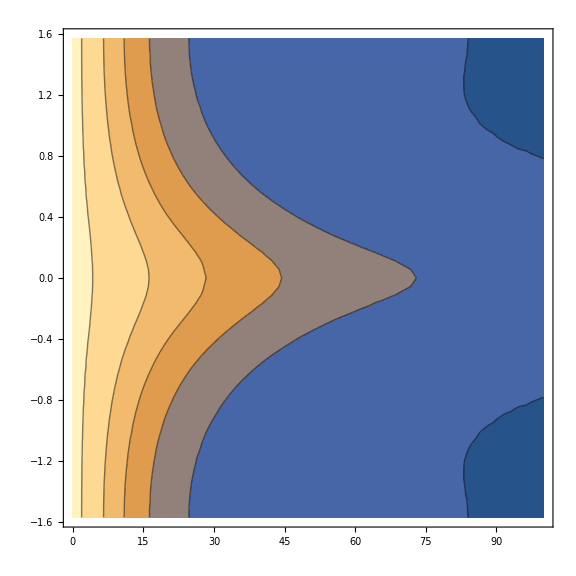
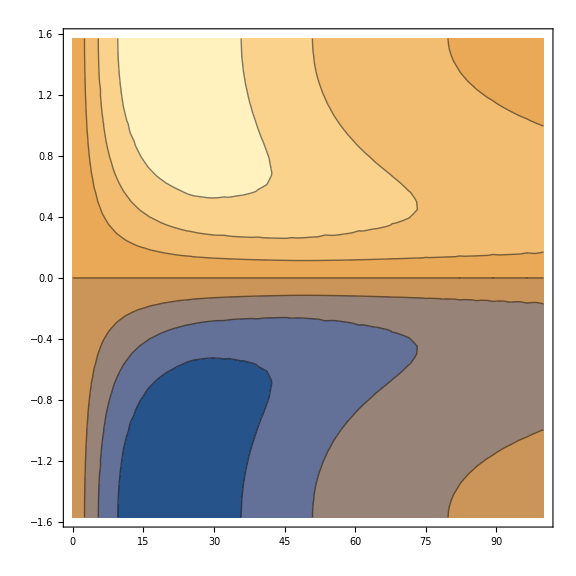
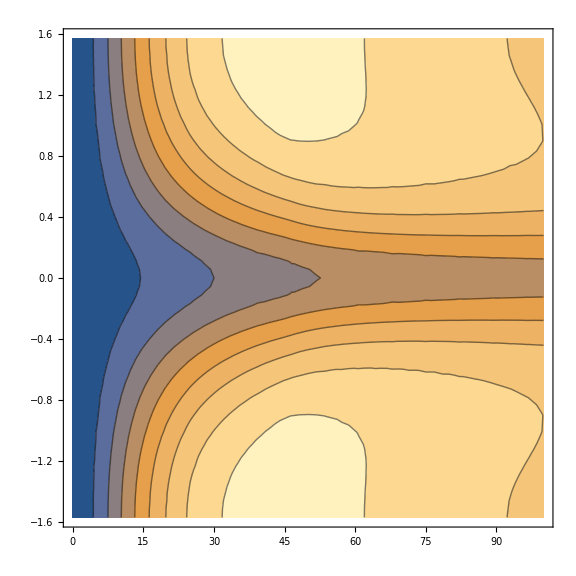
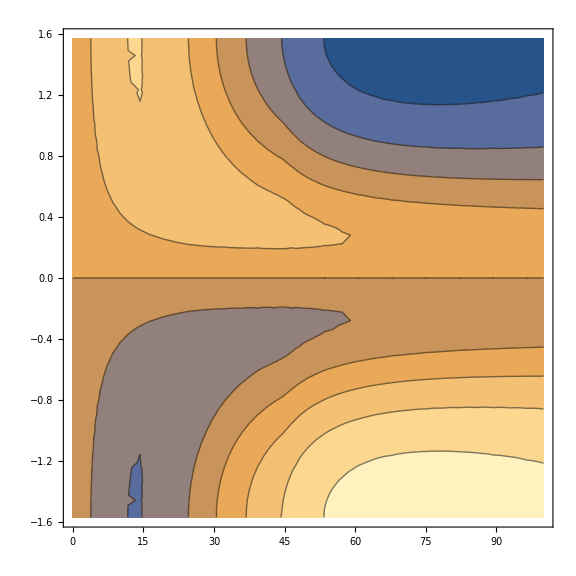
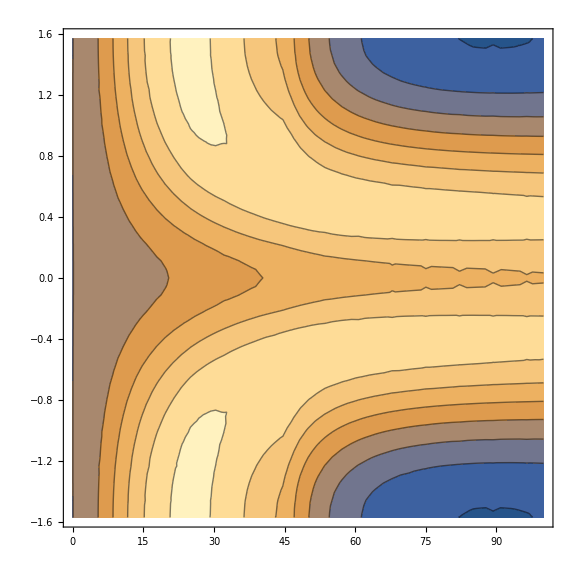
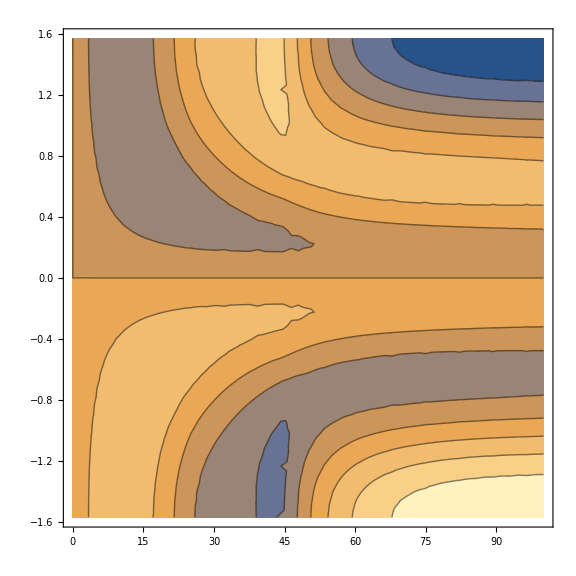
{-Graphics-
-Graphics3D-,-Graphics-
-Graphics3D-,-Graphics-
-Graphics3D-,-Graphics-
-Graphics3D-,-Graphics-
-Graphics3D-,-Graphics-
-Graphics3D-}

```mathematica
Table[
{
ContourPlot[
Re[pef[[i]][ArcTan[r],θ]],
{r,0,100},{θ,-Pi/2,Pi/2},
ImageSize->Large
],
Plot3D[
Re[pef[[i]][ArcTan[r],θ]],
{r,0,100},{θ,-Pi/2,Pi/2},
ImageSize->Large
]
}//TableForm,
{i,6}
]
```

### This time with the proper domain θ ∈ [0,2π) and enforcing PBC

```mathematica
?ndespolar
```

Global`ndespolar

ndespolar[nmax_,mx_,my_,pot_,kappa_,chi_,d_,eps_,maxi_,vn_]:=Module[{tdspt,shift=10,pio2=π/2,stranseps=N[π/2-$MachineEpsilon],evs,efs},tdspt=FullSimplify[FullSimplify[Simplify[-(∂_({x,2},{y,0}) f[x,y])/(2 mx)-(∂_({x,0},{y,2}) f[x,y])/(2 my)+VKeld[kappa][d,chi][x,y] f[x,y]+10 f[x,y]]/.{f→(u[√(#1^2+#2^2),ArcTan[#2/#1]]&)}/.{x→r Cos[θ],y→r Sin[θ]},{-pio2<θ<pio2,0≤r<∞}]/.{u→(g[ArcTan[#1],#2]&)}/.{r→Tan[ψ]},{0≤ψ<π/2}];{evs,efs}=NDEigensystem[{tdspt,DirichletCondition[g[ψ,θ]==0,ψ==pio2],PeriodicBoundaryCondition[g[ψ,θ],θ==0,TranslationTransform[{0,2 π}]]},g[ψ,θ],{ψ,θ}∈Rectangle[{0,0},{pio2,2 π}],nmax,Method→{SpatialDiscretization→{FiniteElement,{MeshOptions→{MaxCellMeasure→eps}}},Eigensystem→{Arnoldi,MaxIterations→maxi},VectorNormalization→vn}];{evs-shift,Head/@efs}]

```mathematica
Clear[pev,pef];
{pev,pef}=ndespolar[6,mx,my,VKeld,4.89,chiphos,0,10^-3,10^12,None];
```

-0.00721344+4.39467×10^-12 ⅈ
-0.00302468+1.37537×10^-14 ⅈ
-0.0012418+6.54077×10^-13 ⅈ
0.00148083-4.32782×10^-11 ⅈ
0.00155247-2.22118×10^-11 ⅈ
0.00443416+1.32904×10^-8 ⅈ

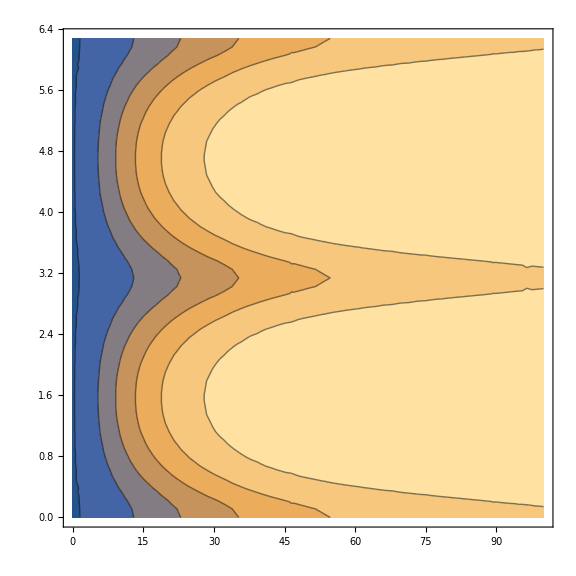
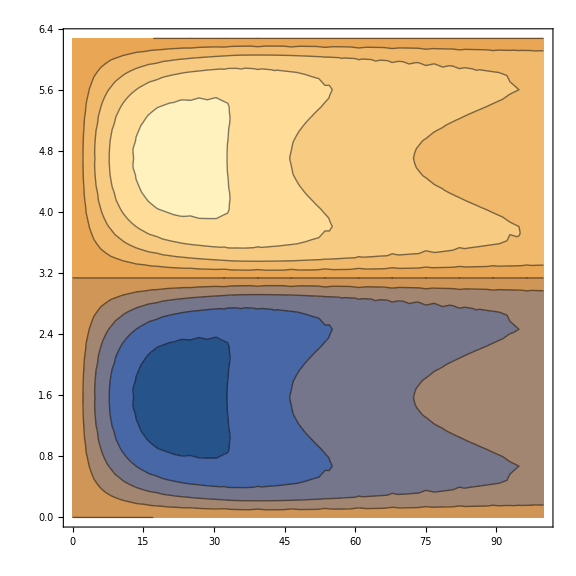
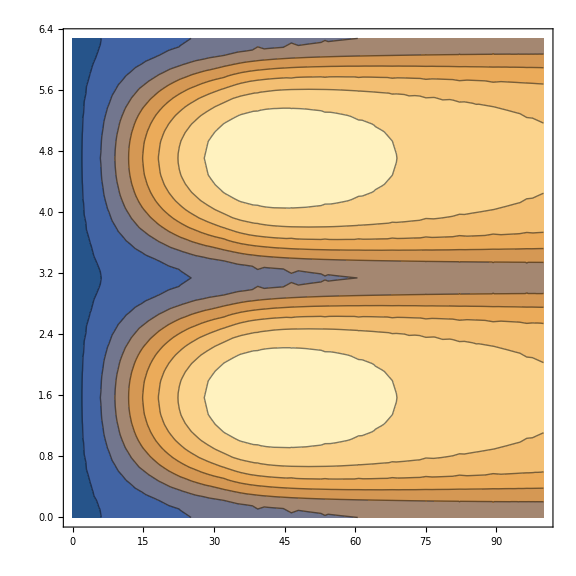
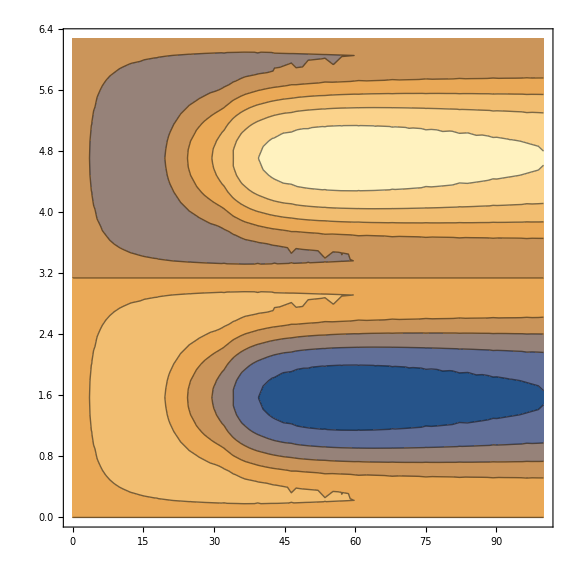
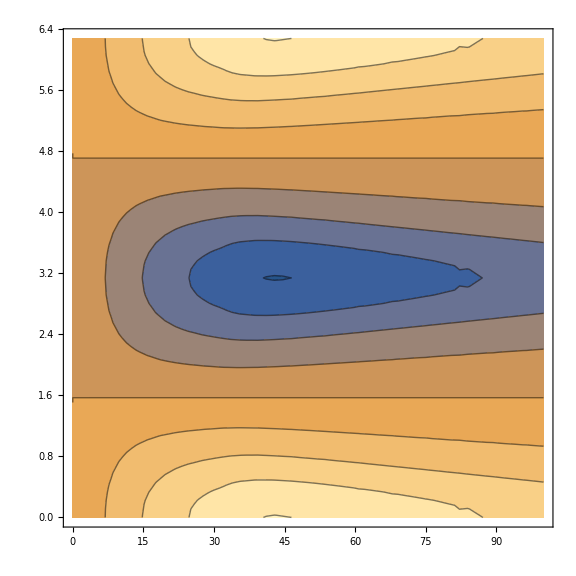
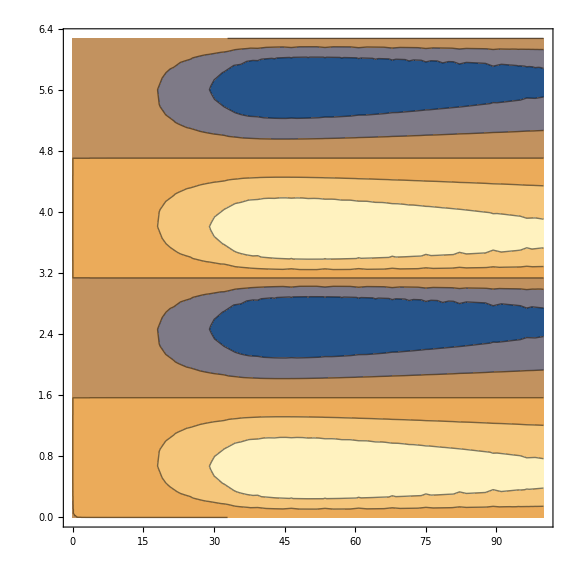
{-Graphics-
-Graphics3D-,-Graphics-
-Graphics3D-,-Graphics-
-Graphics3D-,-Graphics-
-Graphics3D-,-Graphics-
-Graphics3D-,-Graphics-
-Graphics3D-}

```mathematica
TableForm[{pev}//Transpose]
Table[
{
ContourPlot[
Re[pef[[i]][ArcTan[r],θ]],
{r,0,100},{θ,0,2*Pi},
ImageSize->Large
],
Plot3D[
Re[pef[[i]][ArcTan[r],θ]],
{r,0,100},{θ,-0,2*Pi},
ImageSize->Large
]
}//TableForm,
{i,6}
]
```

#### Do the full domain (don’t transform back to r)

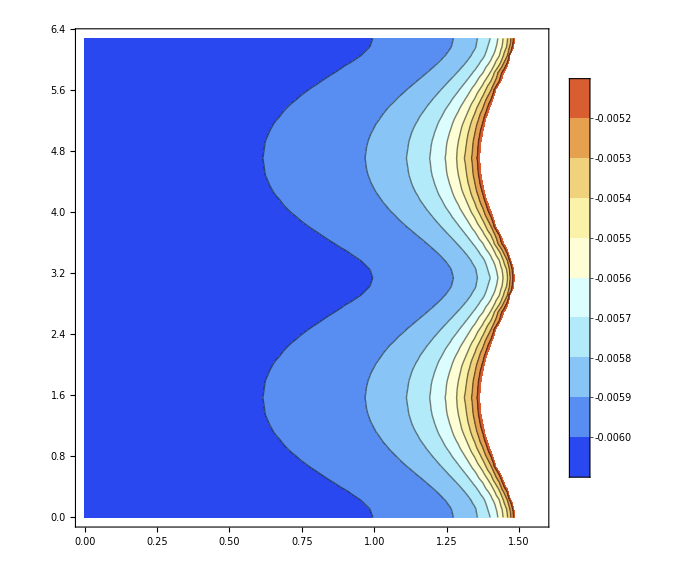
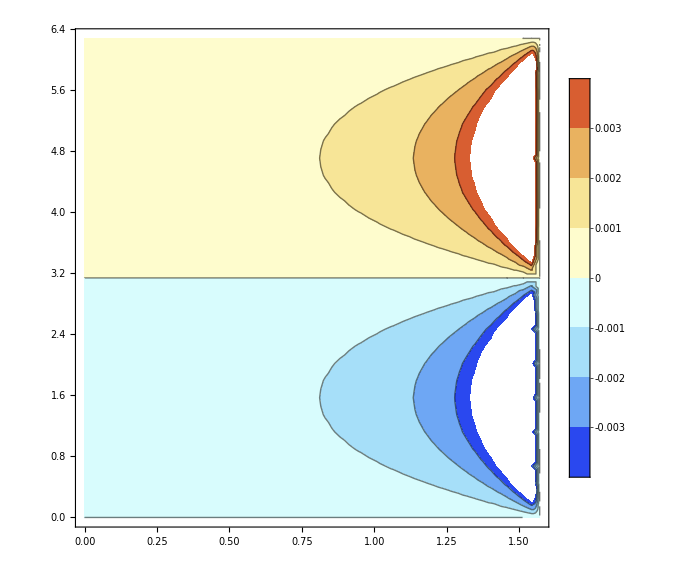
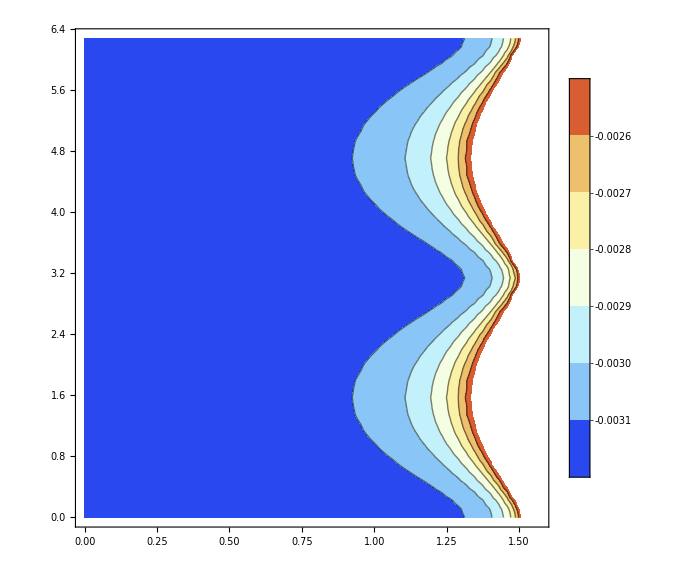
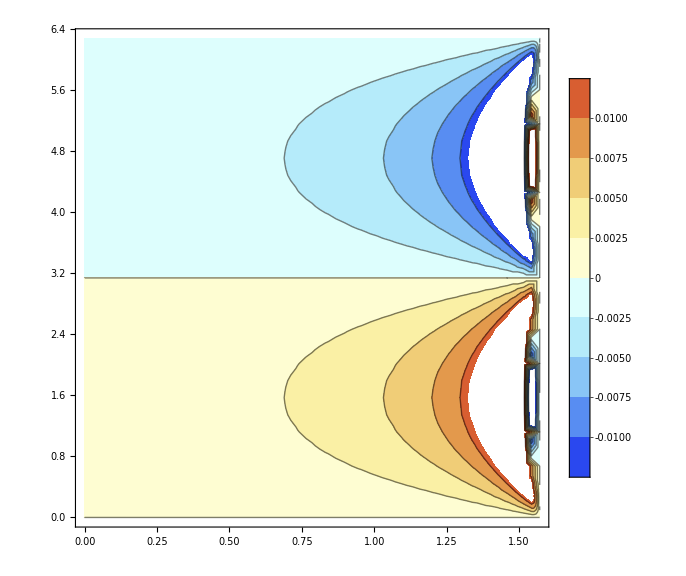
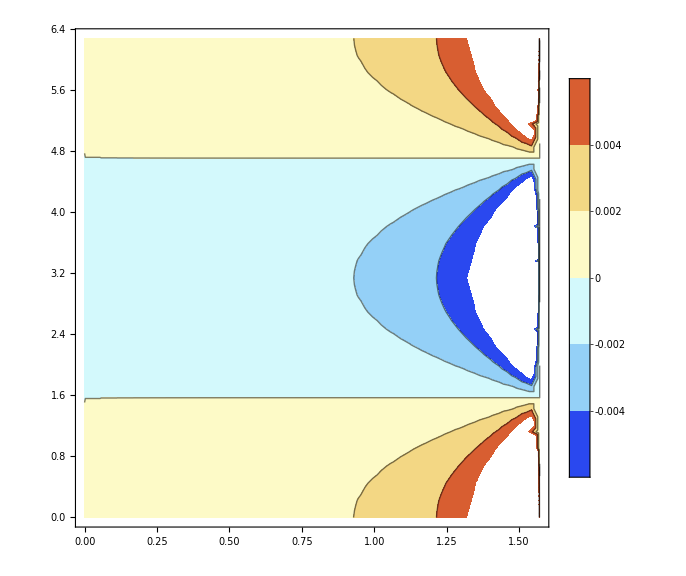
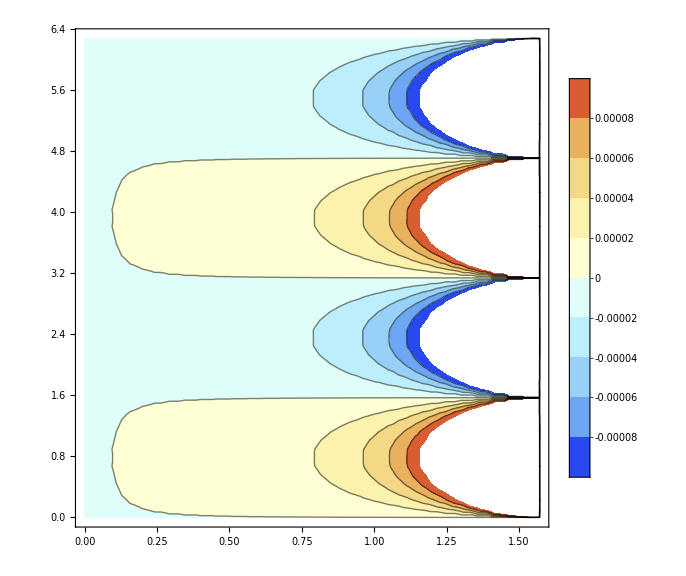
{-Graphics-
-Graphics3D-,-Graphics-
-Graphics3D-,-Graphics-
-Graphics3D-,-Graphics-
-Graphics3D-,-Graphics-
-Graphics3D-,-Graphics-
-Graphics3D-}

```mathematica
Table[
{
ContourPlot[
Re[pef[[i]][ψ,θ]],
{ψ,0,Pi/2},{θ,0,2*Pi},
ImageSize->Large,
ColorFunction->ColorData["LightTemperatureMap"],
ColorFunctionScaling->True,
PlotLegends->Automatic
],
Plot3D[
Re[pef[[i]][ψ,θ]],
{ψ,0,Pi/2},{θ,-0,2*Pi},
ImageSize->Large,
PlotRange->Full
]
}//TableForm,
{i,6}
]
```

#### Looks like the function behaves weirdly as ψ->Pi/2???

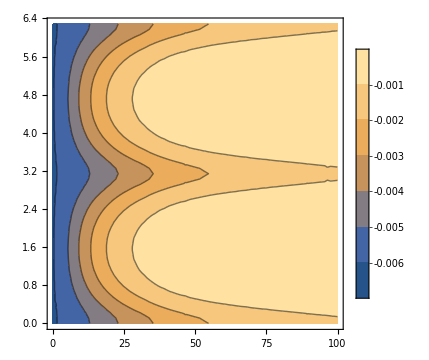
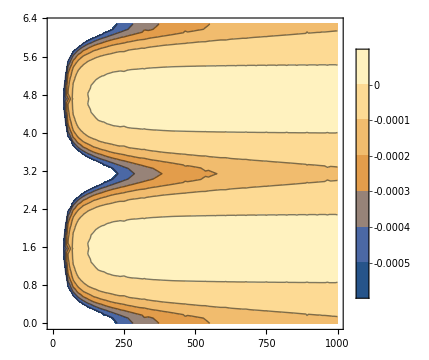
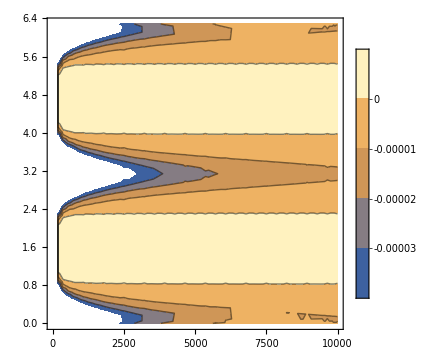
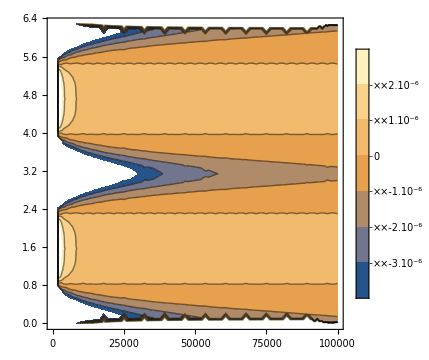
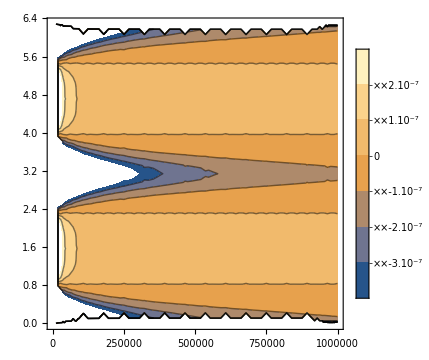

```mathematica
Table[
ContourPlot[
Re[pef[[1]][ArcTan[r],θ]],
{r,0,rmax},{θ,0,2*Pi},
ImageSize->Medium,
PlotLegends->Automatic
],
{rmax,{100,1000,10000,100000,1000000}}
]
```

```mathematica
Table[
Plot3D[
Re[pef[[1]][ArcTan[r],θ]],
{r,0,rmax},{θ,0,2*Pi},
ImageSize->Medium,
PlotLegends->Automatic,
PlotRange->All
],
{rmax,{100,1000,10000,100000,1000000}}
]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Plot3D[
Re[pef[[1]][ArcTan[r],θ]],
{r,0,10^9},{θ,0,2*Pi},
ScalingFunctions->{"Log",None,None},
PlotRange->Full,
ImageSize->Large
]
```

-Graphics3D-

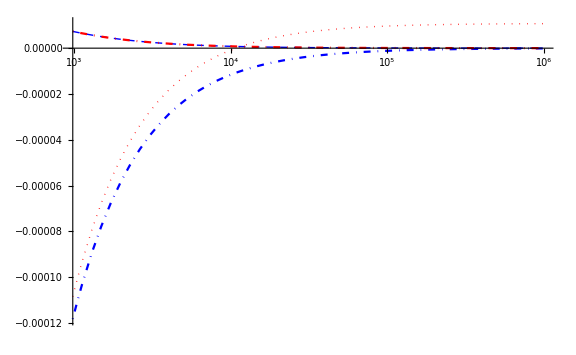

```mathematica
Plot[
Evaluate[Table[Re[pef[[1]][ArcTan[r],θ]],{θ,{0,Pi/2,Pi,3*Pi/2}}]],
{r,0,10^6},
ScalingFunctions->{"Log10",None},
ImageSize->Large,
PlotRange->Full,
PlotStyle->{Directive[Red,Thick,Dotted],Directive[Blue,Thick,Dashed],Directive[Blue,DotDashed],Directive[Red,DotDashed]},
AxesOrigin->{0,0}
]
```

#### Follow the docs exactly

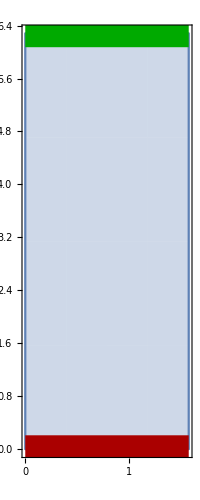

```mathematica
Ω=Rectangle[{0,0},{Pi/2,2*Pi}];
dbc=DirichletCondition[g[ψ,θ]==0,ψ==Pi/2];
f=TranslationTransform[{0,2*Pi}];
Show[RegionPlot[Ω],
Graphics[{Thickness[0.05],#}]&/@{{Darker[Green],TransformedRegion[#,f]},{Darker[Red],#}}&[Line[{{0,0},{Pi/2,0}}]],AspectRatio->Automatic]
```

### Preserve the results above, re-run with minor tweak (need to respect the DBC for θ=0,2*π)

```mathematica
{pev2,pef2}=ndespolar[6,mx,my,VKeld,4.89,chiphos,0,10^-3,10^12,None];
```

-0.00721343+9.44475×10^-12 ⅈ
-0.00302468+2.72333×10^-14 ⅈ
-0.00124177+1.14262×10^-12 ⅈ
0.00148083-7.80273×10^-11 ⅈ
0.00155249-7.97436×10^-12 ⅈ
0.00443416-1.15471×10^-8 ⅈ

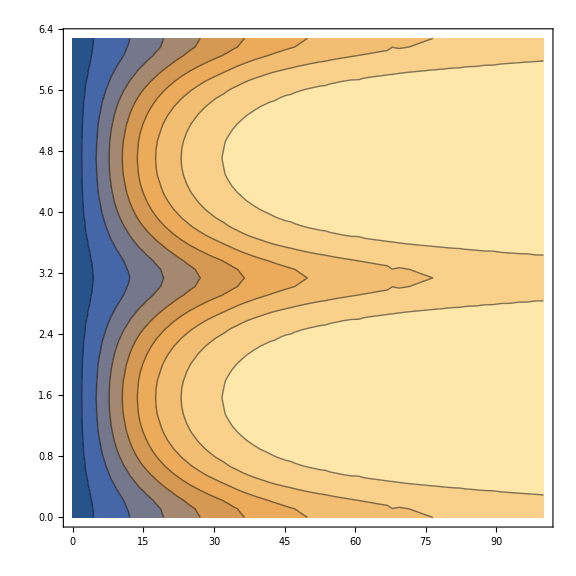
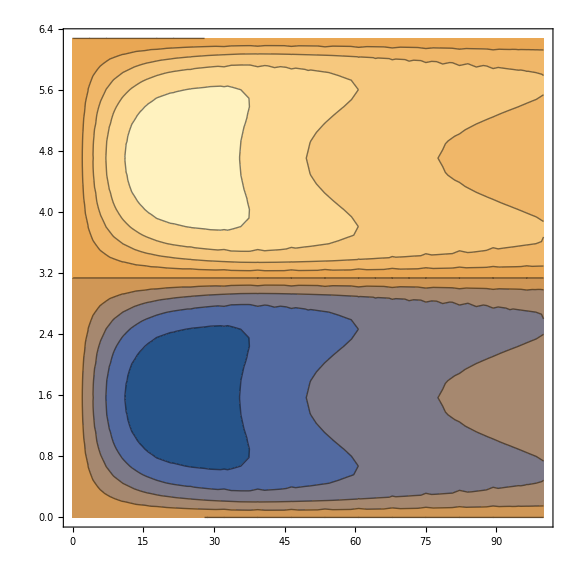
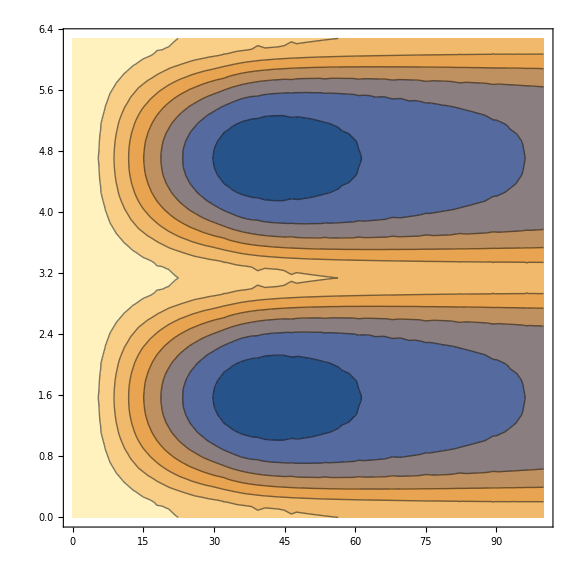
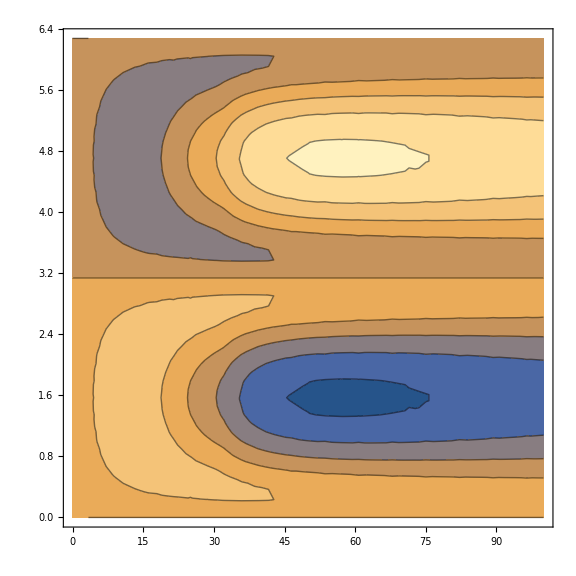
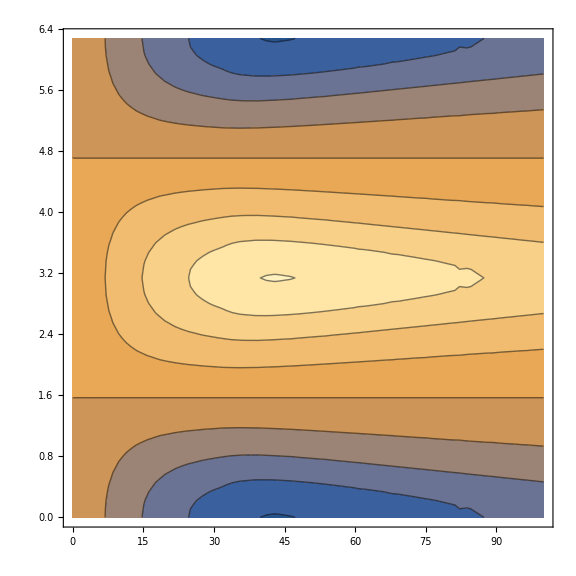
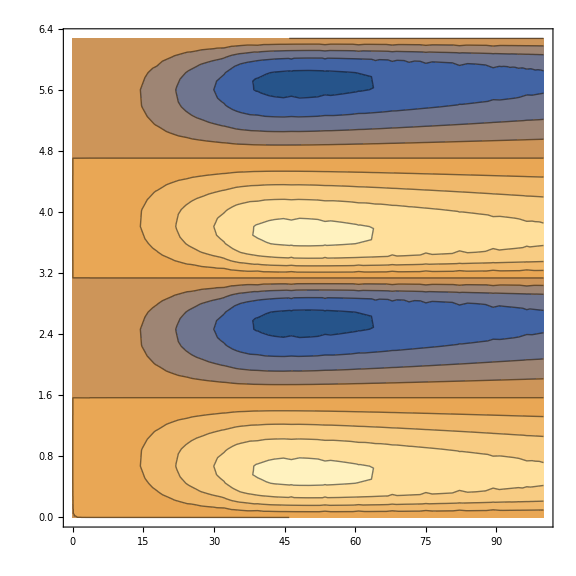
{-Graphics-
-Graphics3D-,-Graphics-
-Graphics3D-,-Graphics-
-Graphics3D-,-Graphics-
-Graphics3D-,-Graphics-
-Graphics3D-,-Graphics-
-Graphics3D-}

```mathematica
TableForm[{pev2}//Transpose]
Table[
{
ContourPlot[
Re[pef2[[i]][ArcTan[r],θ]],
{r,0,100},{θ,0,2*Pi},
ImageSize->Large
],
Plot3D[
Re[pef2[[i]][ArcTan[r],θ]],
{r,0,100},{θ,-0,2*Pi},
ImageSize->Large
]
}//TableForm,
{i,6}
]
```

#### Just a plot taking slices in θ (as before, but now we need all the slices to go to 0)

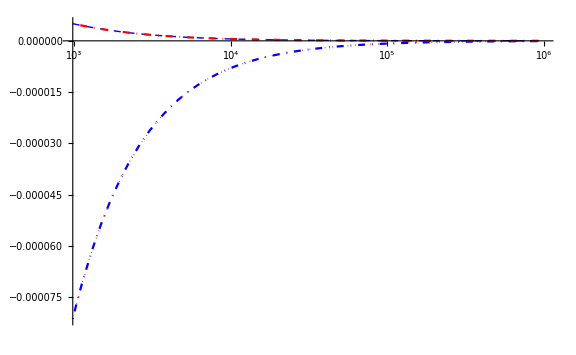
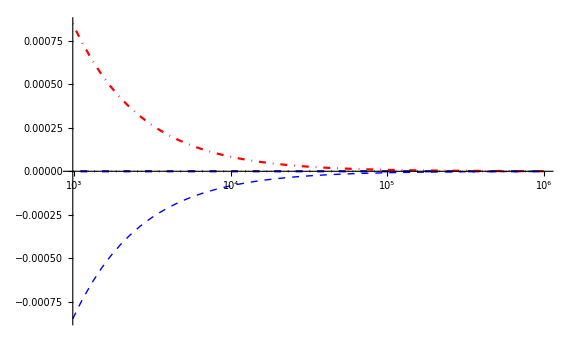
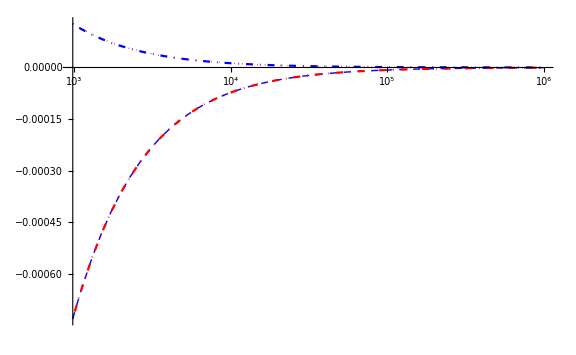
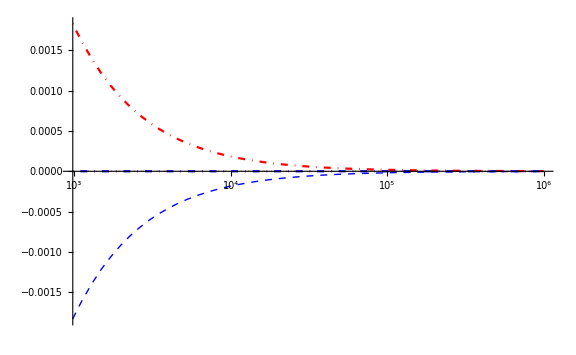
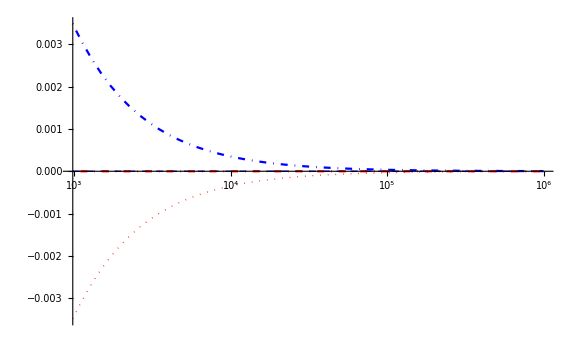
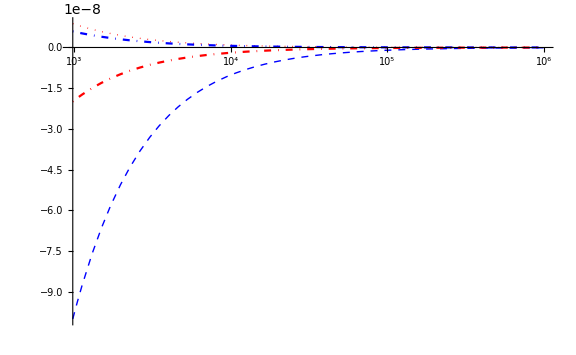

```mathematica
Table[
Plot[
Evaluate[Table[Re[pef2[[n]][ArcTan[r],θ]],{θ,{0,Pi/2,Pi,3*Pi/2}}]],
{r,0,10^6},
ScalingFunctions->{"Log10",None},
ImageSize->Large,
PlotRange->Full,
PlotStyle->{Directive[Red,Thick,Dotted],Directive[Blue,Thick,Dashed],Directive[Blue,DotDashed],Directive[Red,DotDashed]},
AxesOrigin->{0,0}
],
{n,6}]
```

### Getting greedy: now add Neumann BC?

#### Experimenting

```mathematica
NeumannValue
```

NeumannValue

Looks like I just don’t want NeumannValue at all...
Can I just do DirichletCondition[g^(1,0)[ψ,θ]==0,ψ==π/2] ??
Would have to massage that derivative since what I really want is
DirichletCondition[∂_r g[ψ,θ]==0,ψ==π/2]

```mathematica
DirichletCondition[f[x]==0,x==1]
```

DirichletCondition[f[x]==0,x==1]

```mathematica
D[f[x],x]
```

f'[x]

```mathematica
D[f[x],Tan[x]]
```

0

```mathematica
D[f[Tan[x]],x]
```

Sec[x]^2 f'[Tan[x]]

```mathematica
D[u[r,θ],r]
Simplify[D[u[r,θ],r]/.{u->(g[ArcTan[#1],#2]&)}/.{r->Tan[ψ]},{0≤r<Pi/2}]
```

u^(1,0)[r,θ]

Cos[ψ]^2 g^(1,0)[ArcTan[Tan[ψ]],θ]

#### Think I got it, lets try

```mathematica
{pevvn,pefvn}=ndespolar[6,mx,my,VKeld,4.89,chiphos,0,10^-3,10^12,None];
```

NDEigensystem::icfail: Initial condition creation failed.

Set::shape: Lists {evs$1844139,efs$1844139} and NDEigensystem[{«1»},g[ψ,θ],{ψ,θ}∈Rectangle[{0,0},{π/2,2 π}],6,Method→{SpatialDiscretization→{FiniteElement,{MeshOptions→{«1»}}},Eigensystem→{Arnoldi,MaxIterations→1000000000000},VectorNormalization→None}] are not the same shape.

NDEigensystem::icfail: Initial condition creation failed.

```mathematica
TableForm[{pevvn}//Transpose]
Table[
{
ContourPlot[
Re[pefvn[[i]][ArcTan[r],θ]],
{r,0,100},{θ,0,2*Pi},
ImageSize->Large
],
Plot3D[
Re[pefvn[[i]][ArcTan[r],θ]],
{r,0,100},{θ,-0,2*Pi},
ImageSize->Large
]
}//TableForm,
{i,6}
]
```

Transpose::nmtx: The first two levels of {-10+evs$1844139} cannot be transposed.

Transpose[{-10+evs$1844139}]

Part::partd: Part specification efs$1844139⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{-Graphics-
-Graphics3D-,-Graphics-
-Graphics3D-,-Graphics-
-Graphics3D-,-Graphics-
-Graphics3D-,-Graphics-
-Graphics3D-,-Graphics-
-Graphics3D-}

## Cluster isn’t working right now, try running some jobs locally

```mathematica
Table[
Module[
{
rev,ref,stats
},
{{rev,ref},stats}=med[Unevaluated[ndespolar[10,mx,my,VKeld,4.89,chiphos,0,eps[[1]],10^12,None]]];
Export[ToString@StringForm["results/localndepolar/ndepol-nopbc-results_eps`1`.m",eps[[2]]],{rev,ref}];
Export[ToString@StringForm["results/localndepolar/ndepol-nopbc-stats_eps`1`.m",eps[[2]]],stats];
],
{eps,{{10^-3,"1e3"},{5*10^-4,"5e4"},{10^-4,"1e4"},{10^-5,"1e5"}}}
]
```

$Aborted

```mathematica
Export["results/localndepolar/ndepol-nopbc-results_eps9e6.m",ndespolar[10,mx,my,VKeld,4.89,chiphos,0,9*10^-6,10^12,None]]
```

$Aborted

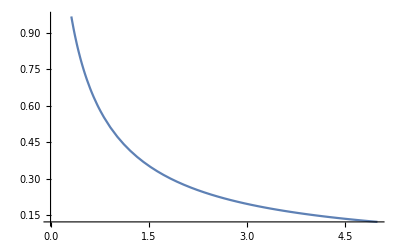

```mathematica
Plot[
StruveH[0,x]-BesselY[0,x],
{x,0,5}
]
```

```mathematica
Quantity[0.85,"Nanometers"]*11/2
Quantity[0.541,"Nanometers"]*11/2
2*Pi*Quantity[0.41,"Nanometers"]
```

4.675 nm

2.9755 nm

2.57611 nm

```mathematica
Quantity[0.227,"Nanometers"]*Cos[13.03Degree]
```

0.221155 nm